gamma-gamma support: on-shell endpoint = 0.170474; Delta_cut = 75 MeV endpoint = 0.238032 GeV^2

pi0-gamma support: on-shell endpoint = 0.300153; Delta_cut = 75 MeV endpoint = 0.387957 GeV^2

Running central calculation with active high-accuracy settings...

level | ggOutsidePercent | pi0gOutsidePercent | totalWidthGeV
medium | 0.732734 | 0.0821047 | 3.50632×10^-10
active | 0.732734 | 0.0821047 | 3.50632×10^-10
strict | 0.732734 | 0.0821047 | 3.50632×10^-10

Running 100 uncertainty replicas...

gamma-gamma on-shell endpoint: (M_eta - m_pi0)^2 = 0.170474 GeV^2

pi0-gamma on-shell endpoint: M_eta^2 = 0.300153 GeV^2

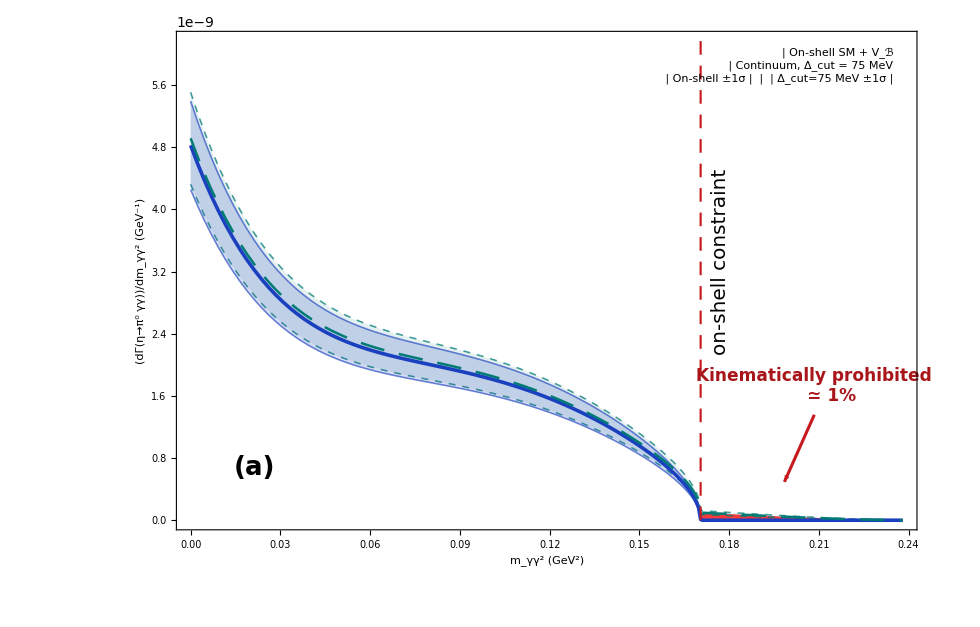

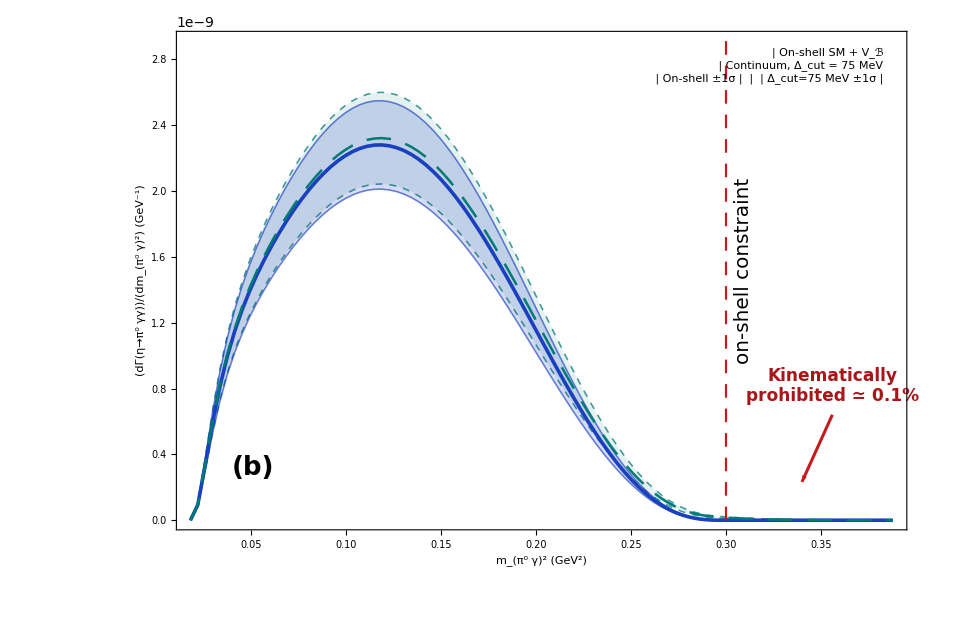

NUMERICAL SUMMARY WITH 1-SIGMA UNCERTAINTIES

Scenario | Width [GeV] | BR | Centroid [GeV] | Mass shift [MeV] | GG outside / total [%] | Pi0G outside / total [%] | GG outside / continuous [%]
SM | 1.670.1410^-10 | 0.0001270.000011 | 0.5478620.000016 | 0. | 0. | 0. | 0.
On-shell VB | 3.40.410^-10 | 0.0002590.000030 | 0.5478620.000016 | 0. | 0. | 0. | 0.
50 MeV | 3.40.410^-10 | 0.0002630.000031 | 0.549450.00027 | 1.590.26 | 0.320.05 | 0.01580.0026 | 3.128440.00029
75 MeV | 3.50.410^-10 | 0.0002680.000032 | 0.55170.0006 | 3.80.6 | 0.730.12 | 0.0820.013 | 6.20560.0005
100 MeV | 3.60.510^-10 | 0.0002750.000034 | 0.55520.0012 | 7.31.2 | 1.390.22 | 0.270.04 | 9.85300.0008

SANITY CHECKS (relative residuals should be near zero)

Dataset[<>]

```mathematica
ClearAll["Global`*"];


nRuns = 100;
nMainGG = 65; nBelowEdgeGG = 25; nAboveEdgeGG = 30; nTailGG = 80;
nMainPiG = 65; nBelowEdgePiG = 25; nAboveEdgePiG = 30; nTailPiG = 90;
accGoal = 10;
precGoal = 8;
maxRec1D = 22;
maxRec2D = 20;
plotImageSize = 900;

integrationMethod = {"GlobalAdaptive", "SymbolicProcessing" -> 0};
ToExpression["integrationScale=10.^12;minRec1D=2;minRec2D=2;$MaxExtraPrecision=2000;SetAttributes[stableNIntegrate,HoldAll];stableNIntegrate[expr_,rest___]:=NIntegrate[integrationScale expr,rest]/integrationScale;"];
EnergyPhotonJEF = 11.0;
cutList = {0.050, 0.075, 0.100};
piGammaMultiplicity = 1;  (* original single-pair convention; use 2 only if both pi0-gamma entries are histogrammed *)

Yukawa2Cs2Ms6MB2CentralInput = 0.0000853727272727272;
Yukawa2Cs2Ms6MB2UncertaintyInput = 0.000010835775045318799;

GenerateValue[M0_?NumericQ, sigma_?NumericQ] :=
  If[sigma == 0, M0, RandomVariate[NormalDistribution[M0, sigma]]];

SetRandomInputs[central_: False] := Module[{draw},
  draw[M0_?NumericQ, sigma_?NumericQ] :=
    If[TrueQ[central], M0, GenerateValue[M0, sigma]];

  CoupleEff = draw[Yukawa2Cs2Ms6MB2CentralInput,
    Yukawa2Cs2Ms6MB2UncertaintyInput];
  BestYukawa2Cs2Ms6MB2 = CoupleEff;

  ΓMAMI = draw[0.33*10^(-9), 0.03*10^(-9)];
  Δα = 0.000000017*10^(-3);
  α = draw[7.297525664*10^(-3), Δα];
  fK = 110.10*10^(-3);
  fπ = 92.07*10^(-3);

  ΔΓtotal = 0.05*10^(-6);
  Γtotal = draw[1.31*10^(-6),
    ΔΓtotal];
  ΔBR = 0.22*10^(-4);
  BR = draw[2.56*10^(-4), ΔBR];

  Δmπ = 0.0005*10^(-3);
  mπ = draw[134.9768*10^(-3), Δmπ];
  ΔmπA = 0.00018*10^(-3);
  mπA = draw[139.57039*10^(-3), ΔmπA];
  ΔMη = 0.017*10^(-3);
  Mη = draw[547.862*10^(-3), ΔMη];

  Δmρ = 0.23*10^(-3);
  mρ = draw[775.26*10^(-3), Δmρ];
  Δmω = 0.13*10^(-3);
  mω = draw[782.66*10^(-3), Δmω];
  Δmϕ = 0.016*10^(-3);
  mϕ = draw[1019.461*10^(-3), Δmϕ];

  ΔΓω = 0.13*10^(-3);
  Γω = draw[8.68*10^(-3),
    ΔΓω];
  ΔΓρ = 0.8*10^(-3);
  Γρ = draw[149.1*10^(-3),
    ΔΓρ];
  ΔΓϕ = 0.013*10^(-3);
  Γϕ = draw[4.249*10^(-3),
    ΔΓϕ];

  maZero = 980*10^(-3);
  ΔmKP = 0.016*10^(-3);
  mKP = draw[493.677*10^(-3), ΔmKP];

  (* IMPORTANT: one and the same proton mass is used in the contact
     matrix element and in gamma-p production kinematics. The uncertainty
     is 0.00000029 MeV = 2.9 10^-10 GeV, not 0.00029 GeV. *)
  mProton = draw[938.27208943*10^(-3), 0.00000029*10^(-3)];
  mN = mProton;
  sIncomingJEF = mProton^2 + 2*mProton*EnergyPhotonJEF;
  sIncoming = sIncomingJEF;

  Δg = 0.01;
  g = draw[0.70, Δg];
  ΔzSmBm = 0.01;
  zSmBm = draw[0.65, ΔzSmBm];
  ΔϕP = 0.5;
  ϕP = draw[41.4, ΔϕP] Degree;
  ΔϕV = 0.1;
  ϕV = draw[3.3, ΔϕV] Degree;
  ΔzNS = 0.02;
  zNS = draw[0.83, ΔzNS];

  gρπγ = g/3;
  gρηγ = g*zNS*Cos[ϕP];
  gωπγ = g*Cos[ϕV];
  gωηγ = g/3*(zNS*Cos[ϕP]*Cos[ϕV] -
    2*zSmBm*Sin[ϕP]*Sin[ϕV]);
  gϕπγ = g*Sin[ϕV];
  gϕηγ = g/3*(zNS*Cos[ϕP]*Sin[ϕV] +
    2*zSmBm*Sin[ϕP]*Cos[ϕV]);

  cρ = gρπγ*gρηγ;
  cω = gωπγ*gωηγ;
  cϕ = gϕπγ*gϕηγ;

  ga0KKbarSq = (-maZero^2 + mKP^2)^2/(2*fK^2);
  ga0πηSq = ((-maZero^2 + Mη^2)^2*Cos[ϕP]^2)/fπ^2;
];

ProgressStatus[label_, i_, total_] := Row[{label, ": ",
  ProgressIndicator[i, {0, total}], "  ", i, "/", total}];

SetRandomInputs[True];
(* ============================================================*)
(*2. Kinematics and SM amplitude ingredients*)
(* ============================================================*)

ΓρEff[
         t_] := Γρ*((-4 mπA^2 + 
        t)/(-4 mπA^2 + 
                        mρ^2))^(3/2)*
   HeavisideTheta[-4 mπA^2 + t];

m232MAX[m132_] := (Mη^2 + 
                     
              
       mπ^2)^2/(4 m132) - (-((-m132 + Mη^2)/(2 Sqrt[m132])) +
                   Sqrt[-mπ^2 + (m132 + mπ^2)^2/(4 m132)])^2;

m232MIN[m132_] := (Mη^2 + 
                     
              
       mπ^2)^2/(4 m132) - ((-m132 + Mη^2)/(2 Sqrt[m132]) + 
                  Sqrt[-mπ^2 + (m132 + mπ^2)^2/(4 m132)])^2;

Constraint[m132_, m232_] := 
      HeavisideTheta[m232MAX[m132] - m232]*
         HeavisideTheta[m232 - m232MIN[m132]];

AtSM[t_?NumericQ] := 
  cρ/(-t + mρ^2 - I*mρ*ΓρEff[t]) + 
   cϕ/(-t + mϕ^2 - I*mϕ*Γϕ) + 
   cω/(-t + mω^2 - I*mω*Γω);

AuSM[u_?NumericQ] := 
  cρ/(-u + mρ^2 - I*mρ*ΓρEff[u]) + 
   cϕ/(-u + mϕ^2 - I*mϕ*Γϕ) + 
   cω/(-u + mω^2 - I*mω*Γω);

DarkContact[Yukawa2Cs2Ms6MB2_?NumericQ] := 
  Yukawa2Cs2Ms6MB2*((4*64*mN^6)/α)*cω;

AtDark[t_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ] := 
  AtSM[t] + DarkContact[Yukawa2Cs2Ms6MB2];

AuDark[u_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ] := 
  AuSM[u] + DarkContact[Yukawa2Cs2Ms6MB2];

Bq2Bq2p[m132_, m232_] := 
      1/8 (m132^2 + 
      Mη^4) (-m132 - m232 + Mη^2 + mπ^2)^2 + 
         1/8 (-m132 + Mη^2) (-m232 + Mη^2)*(m132 m232 + 
                  Mη^2 (m132 + m232 - Mη^2 - 2 mπ^2));

Bq1Bq1[m132_, m232_] := 
      1/8 (m232^2 + 
      Mη^4) (-m132 - m232 + Mη^2 + mπ^2)^2 + 
         1/8 (-m132 + Mη^2) (-m232 + Mη^2)*(m132 m232 + 
                  Mη^2 (m132 + m232 - Mη^2 - 2 mπ^2));

Bq2Bq1[m132_, m232_] := 
      1/8 (m132*m232 + 
                  Mη^4) (-m132 - m232 + Mη^2 + mπ^2)^2 + 
         1/8 (-m132 + Mη^2) (-m232 + Mη^2)*(m132 m232 + 
                  Mη^2 (m132 + m232 - Mη^2 - 2 mπ^2));

BWt[m132_, m232_] := 
      Abs[cρ/(-m132 + mρ^2 - 
                        I mρ*ΓρEff[m132]) + 
               
          
     cϕ/(-m132 + mϕ^2 - I mϕ*Γϕ) + 
               cω/(-m132 + mω^2 - 
                        I mω*Γω)]^2;

BWu[m132_, m232_] := 
      Abs[cρ/(-m232 + mρ^2 - 
                        I mρ*ΓρEff[m232]) + 
               
          
     cϕ/(-m232 + mϕ^2 - I mϕ*Γϕ) + 
               cω/(-m232 + mω^2 - 
                        I mω*Γω)]^2;

BWtu[m132_, m232_] := 
      Re[(cρ/(-m132 + mρ^2 - 
                           I mρ*ΓρEff[m132]) + 
                  
            
      cϕ/(-m132 + mϕ^2 - I mϕ*Γϕ) + 
                  cω/(-m132 + mω^2 - 
                           
                  
         I mω*Γω))*(cρ/(-m232 + 
                           mρ^2 + 
                  I mρ*ΓρEff[m232]) + 
                  
            
      cϕ/(-m232 + mϕ^2 + I mϕ*Γϕ) + 
                  cω/(-m232 + mω^2 + 
                           I mω*Γω))];

MatrixVMD[m132_, 
         m232_] := (Bq2Bq2p[m132, m232]*BWt[m132, m232] + 
               2*Bq2Bq1[m132, m232]*BWtu[m132, m232] + 
               Bq1Bq1[m132, m232]*BWu[m132, m232])*
   Constraint[m132, m232];

(* ============================================================*)
(*3. LSM/scalar-sector pieces*)
(* ============================================================*)

βPlusπη[s_] := Sqrt[1 - (Mη + mπ)^2/s];
βMinusπη[s_] := Sqrt[1 - (Mη - mπ)^2/s];

βBarPlusπη[s_] := Sqrt[-1 + (Mη + mπ)^2/s];
βBarMinusπη[s_] := Sqrt[-1 + (-Mη + mπ)^2/s];

βK[s_] := Sqrt[1 - (4*mKP^2)/s];
βKbar[s_] := Sqrt[(4*mKP^2)/s - 1];

θπη[s_] := HeavisideTheta[-(Mη + mπ)^2 + s];

Barθπη[s_] := 
      HeavisideTheta[(Mη + mπ)^2 - s]*
         HeavisideTheta[-(-Mη + mπ)^2 + s];

BarBarθπη[s_] := 
      HeavisideTheta[(-Mη + mπ)^2 - s];

θK[s_] := HeavisideTheta[-4*mKP^2 + s];
θKbar[s_] := HeavisideTheta[4*mKP^2 - s];

R1[s_] := 
      ga0KKbarSq/(16 π^2)*(2 - 
               
          
     Log[(1 + βK[s])/(1 - βK[s])]*βK[s]*θK[
                     s] - 
          2 ArcTan[1/βKbar[s]]*βKbar[s]*θKbar[s]);

R2[s_] := 
      ga0πηSq/(16 π^2)*(2 - ((Mη^2 - mπ^2)*
                        Log[Mη/mπ])/s - 
               
     Log[(βMinusπη[s] + βPlusπη[
                                 s])/(βMinusπη[
                      s] - βPlusπη[
                                 s])]*βMinusπη[
              s]*βPlusπη[
                     s]*θπη[s]);

R3[s_] := 
      ga0πηSq/(16 π^2)*(BarBarθπη[s]*
                  
            
      Log[(βBarMinusπη[s] + βBarPlusπη[
                                 s])/(-βBarMinusπη[
                                    s] + βBarPlusπη[
                                 s])]*βBarMinusπη[
                     s]*βBarPlusπη[s] - 
               
          
     2*ArcTan[βMinusπη[s]/βBarPlusπη[
                           s]]*
                  Barθπη[s]*βBarPlusπη[
                     s]*βMinusπη[s]);

R[s_] := R1[s] + R2[s] + R3[s];

ImaginaryPart[
         s_] := -((ga0KKbarSq*βK[s]*θK[s])/(16 π)) - 
         1/(16 π)*
            ga0πηSq*βPlusπη[
               s]*βMinusπη[s]*θπη[s];

Da0[s_] := -maZero^2 + s + R[s] - R[maZero^2] + I*ImaginaryPart[s];

ALSM[s_] := 
      1/(2*fK*fπ)*((-Mη^2 + s)*((-maZero^2 + mKP^2)/Da0[s])*
                  Cos[ϕP] + 
               1/6*((5 Mη^2 + mπ^2 - 3 s)*Cos[ϕP] - 
                        
                
        Sqrt[2]*(4 mKP^2 + Mη^2 + mπ^2 - 3 s)*Sin[ϕP]));

f[z_] := 1/4*
            HeavisideTheta[
               1/4 - z]*(-I π + 
                     Log[(1 + Sqrt[1 - 4 z])/(1 - Sqrt[1 - 4 z])])^2 - 
         ArcSin[1/(2 Sqrt[z])]^2*HeavisideTheta[-(1/4) + z];

(* Numerically stable kaon-loop function.  The direct expression is an
   exact 0/0 cancellation at z = 0 and loses precision for very small z.
   The analytic expansion is
      L(z) = 1/24 + z/180 + z^2/1120 + z^3/6300 + O(z^4). *)
L[z_?NumericQ] := Which[
  Abs[z] < 10^-6,
    1/24 + z/180 + z^2/1120 + z^3/6300,
  True,
    -(1/(2 z)) - (2 f[1/z])/z^2
];

(* ============================================================*)
(*Interference and LSM squared piece*)
(* ============================================================*)
(*This is 2*Re[LσM*VMD^+]*)
ClearAll[Int1VMDLSM, Int2VMDLSM, Interference, LSM, Int1VMDLSMDARK, 
  Int2VMDLSMDARK, InterferenceDARK];

Int1VMDLSM[m132_?NumericQ, 
   m232_?NumericQ] := -(α/(π*mKP^2))*
   L[(-m132 - m232 + Mη^2 + mπ^2)/mKP^2]*
   ALSM[-m132 - m232 + Mη^2 + mπ^2];

Int2VMDLSM[m132_?NumericQ, m232_?NumericQ] := 
  Conjugate[(m132*AtSM[m132] + m232*AuSM[m232])]*(-m132 - m232 + 
      Mη^2 + mπ^2)^2;

Interference[m132_?NumericQ, m232_?NumericQ] := 
  Re[Int1VMDLSM[m132, m232]*Int2VMDLSM[m132, m232]]*
   Constraint[m132, m232];
(*Note that the factor of 2 is taken into account, so Interference = \
2*Re[LσM*VMD^+]*)
(*This is LσM Squared*)

(*Factor of 2 because {a}^2 = 2(q1*q2)*)
LSM[m132_?NumericQ, 
   m232_?NumericQ] := ((2*α^2)/(π^2*mKP^4))*((-m132 - 
       m232 + Mη^2 + mπ^2)^2)*
   Abs[ALSM[-m132 - m232 + Mη^2 + mπ^2]*
      L[(-m132 - m232 + Mη^2 + mπ^2)/mKP^2]]^2*
   Constraint[m132, m232];

(* ============================================================*)
(*4. SM spectra*)
(* ============================================================*)

γγSpectrum[m122_] := 
      stableNIntegrate[(1/
                  2)*1/(256 Mη^3 π^3)*(MatrixVMD[m132, 
                     Mη^2 + mπ^2 - m132 - m122] + 
                  
      Interference[m132, Mη^2 + mπ^2 - m132 - m122] + 
                  LSM[m132, Mη^2 + mπ^2 - m132 - m122])*
            
    Constraint[m132, Mη^2 + mπ^2 - m132 - m122], {m132, 
            mπ^2, Mη^2}, AccuracyGoal -> accGoal, 
         Method -> {"AdaptiveQuasiMonteCarlo"}, 
   MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D];

πγIntegral[m132_] := 
      stableNIntegrate[
         MatrixVMD[m132, m232] + Interference[m132, m232] + 
            LSM[m132, m232], {m232, mπ^2, Mη^2}, 
         AccuracyGoal -> accGoal, 
   Method -> {"AdaptiveQuasiMonteCarlo"}, 
         MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D];

πγSpectrum[
         m132_] := (1/
     2)*1/(256 Mη^3 π^3)*πγIntegral[
            m132];

(* ============================================================*)
(*5. Dark/SM+V_B spectra*)
(* ============================================================*)

BWtDARK[m132_, m232_, Yukawa2Cs2Ms6MB2_] := 
      Abs[cρ/(-m132 + mρ^2 - 
                        I mρ*ΓρEff[m132]) +
     cϕ/(-m132 + mϕ^2 - I mϕ*Γϕ) + 
               cω/(-m132 + mω^2 - 
                        I mω*Γω) + 
               Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω]^2;
BWuDARK[m132_, m232_, Yukawa2Cs2Ms6MB2_] := 
      Abs[cρ/(-m232 + mρ^2 - 
                        I mρ*ΓρEff[m232]) + 
     cϕ/(-m232 + mϕ^2 - I mϕ*Γϕ) + 
               cω/(-m232 + mω^2 - 
                        I mω*Γω) + 
               Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω]^2;

BWtuDARK[m132_, m232_, Yukawa2Cs2Ms6MB2_] := 
      Re[(cρ/(-m132 + mρ^2 - 
                           I mρ*ΓρEff[m132]) + 
      cϕ/(-m132 + mϕ^2 - I mϕ*Γϕ) + 
                  cω/(-m132 + mω^2 - 
                           I mω*Γω) + 
                  Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*
                     cω)*(cρ/(-m232 + mρ^2 + 
                           I mρ*ΓρEff[m232]) + 
      cϕ/(-m232 + mϕ^2 + I mϕ*Γϕ) + 
                  cω/(-m232 + mω^2 + 
                           I mω*Γω) + 
                  Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω)];

MatrixVMDDARK[m132_, m232_, 
         Yukawa2Cs2Ms6MB2_] := (Bq2Bq2p[m132, m232]*
                  BWtDARK[m132, m232, Yukawa2Cs2Ms6MB2] + 
     2*Bq2Bq1[m132, m232]*BWtuDARK[m132, m232, Yukawa2Cs2Ms6MB2] +              
     Bq1Bq1[m132, m232]*BWuDARK[m132, m232, Yukawa2Cs2Ms6MB2])*
         Constraint[m132, m232];

Int1VMDLSMDARK[m132_, m232_, 
         Yukawa2Cs2Ms6MB2_] := (2 α)/(π*mKP^2)*
         L[(-m132 - m232 + Mη^2 + mπ^2)/mKP^2]*
         ALSM[-m132 - m232 + Mη^2 + mπ^2];

Int2VMDLSMDARK[m132_, m232_, 
         Yukawa2Cs2Ms6MB2_] := -Conjugate[
            1/4 (-m132 - m232 + Mη^2 +           
        mπ^2)^2*(m132*(cρ/(-m132 + mρ^2 -                            
             I mρ*ΓρEff[m132]) + 
                              cϕ/(-m132 + mϕ^2 -                          
             I mϕ*Γϕ) + 
                              cω/(-m132 + mω^2 -                   
             I mω*Γω) + 
 Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω) + 
                     m232*(cρ/(-m232 + mρ^2 -                  
             I mρ*ΓρEff[m232]) + 
                              cϕ/(-m232 + mϕ^2 - 
                                       
             I mϕ*Γϕ) + 
                              cω/(-m232 + mω^2 - 
                                       
             I mω*Γω) + 
                              
          Yukawa2Cs2Ms6MB2*(4*64 mN^6)/α*cω))];

InterferenceDARK[m132_, m232_, Yukawa2Cs2Ms6MB2_] := 
      2*Re[Int1VMDLSMDARK[m132, m232, Yukawa2Cs2Ms6MB2]*
               Int2VMDLSMDARK[m132, m232, Yukawa2Cs2Ms6MB2]]*
         Constraint[m132, m232];

γγSpectrumDARK[m122_, Yukawa2Cs2Ms6MB2_] := 
      stableNIntegrate[(1/
                  2)*1/(256 Mη^3 π^3)*(MatrixVMDDARK[m132, 
                     Mη^2 + mπ^2 - m132 - m122, 
       Yukawa2Cs2Ms6MB2] + 
                  
      InterferenceDARK[m132, Mη^2 + mπ^2 - m132 - m122, 
                     Yukawa2Cs2Ms6MB2] + 
                  LSM[m132, Mη^2 + mπ^2 - m132 - m122])*
            
    Constraint[m132, Mη^2 + mπ^2 - m132 - m122], {m132, 
            mπ^2, Mη^2}, AccuracyGoal -> accGoal, 
         Method -> {"AdaptiveQuasiMonteCarlo"}, 
         MaxRecursion -> maxRec1DDark];

πγIntegrandDark[m132_, Yukawa2Cs2Ms6MB2_] := 
      stableNIntegrate[
         MatrixVMDDARK[m132, m232, Yukawa2Cs2Ms6MB2] + 
            InterferenceDARK[m132, m232, Yukawa2Cs2Ms6MB2] + 
            LSM[m132, m232], {m232, mπ^2, Mη^2}, 
         AccuracyGoal -> accGoal, 
   Method -> {"AdaptiveQuasiMonteCarlo"}, 
         MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D];

πγSpectrumDark[m132_, 
         Yukawa2Cs2Ms6MB2_] := (1/
               2)*1/(256 Mη^3 π^3)*πγIntegrandDark[
        m132, 
            Yukawa2Cs2Ms6MB2];

(* ============================================================*)
(*5b. Pure continuous V_B^2 contact contribution*)
(* ============================================================*)

ClearAll[
  AloneBWtDARK, AloneBWuDARK, AloneBWtuDARK,
  MatrixVMDaloneDARK
];

(*
  This is only the standalone contact-contact contribution |D|^2.
  It removes the purely smooth V_B^2 continuum from the full SM+V_B result.
  The t-u cross term is Re[D D^*] = |D|^2, not |D|.
*)

AloneBWtDARK[
   m132_?NumericQ, m232_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ
   ] := Abs[DarkContact[Yukawa2Cs2Ms6MB2]]^2;

AloneBWuDARK[
   m132_?NumericQ, m232_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ
   ] := Abs[DarkContact[Yukawa2Cs2Ms6MB2]]^2;

AloneBWtuDARK[
   m132_?NumericQ, m232_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ
   ] := Abs[DarkContact[Yukawa2Cs2Ms6MB2]]^2;

MatrixVMDaloneDARK[
   m132_?NumericQ, m232_?NumericQ, Yukawa2Cs2Ms6MB2_?NumericQ
   ] :=
  (
    Bq2Bq2p[m132, m232]*
      AloneBWtDARK[m132, m232, Yukawa2Cs2Ms6MB2]
    +
    2*Bq2Bq1[m132, m232]*
      AloneBWtuDARK[m132, m232, Yukawa2Cs2Ms6MB2]
    +
    Bq1Bq1[m132, m232]*
      AloneBWuDARK[m132, m232, Yukawa2Cs2Ms6MB2]
  )*Constraint[m132, m232];

(* ============================================================ *)
(* 6. Continuous V_B^2 contribution and exact physical limits  *)
(* ============================================================ *)

ClearAll[
  KallenPub, Omega2Pub, GGtMin, GGtMax, PiGuMin, PiGuMax,
  MxBq2Bq2p, MxBq1Bq1, MxBq2Bq1,
  ContinuousVBAloneMatrixVMDDARK,
  OnShellSMKernel, OnShellDarkKernel, OnShellPureVBKernel,
  OnShellEffectiveKernel,
  OnShellGGSpectrumSM, OnShellGGSpectrumDark,
  OnShellGGSpectrumPureVB, OnShellGGSpectrumEffective,
  OnShellPiGammaSpectrumSM, OnShellPiGammaSpectrumDark,
  OnShellPiGammaSpectrumPureVB, OnShellPiGammaSpectrumEffective,
  FixedMxPureGGSpectrum, FixedMxPurePiGammaSpectrum,
  OnShellWidthSMValue, OnShellWidthDarkValue,
  OnShellWidthPureVBValue, OnShellWidthEffectiveValue,
  FixedMxPureVBWidth, ProductionNormalization,
  ContinuousPureGGSpectrum, ContinuousPurePiGammaSpectrum,
  ContinuousModelGGSpectrum, ContinuousModelPiGammaSpectrum,
  ContinuousPureWidth, ContinuousPureMassMoment,
  FixedMxProhibitedGGWidth, FixedMxProhibitedPiGammaWidth,
  ContinuousProhibitedGGWidth, ContinuousProhibitedPiGammaWidth
];

KallenPub[x_?NumericQ, y_?NumericQ, z_?NumericQ] :=
  x^2 + y^2 + z^2 - 2*x*y - 2*x*z - 2*y*z;

Omega2Pub[Mx_?NumericQ, sIn_?NumericQ] := Module[{lam},
  lam = KallenPub[sIn, mProton^2, Mx^2];
  If[lam <= 0., 0., Sqrt[lam]/(8*Pi*sIn)]
];

(* Fixed s_gg = m_gg^2, integrate t = m_pi0gamma^2. *)
GGtMin[Mx_?NumericQ, sgg_?NumericQ] := Module[{lam},
  lam = Max[0., KallenPub[Mx^2, mπ^2, sgg]];
  mπ^2 + (Mx^2 - mπ^2 - sgg - Sqrt[lam])/2
];

GGtMax[Mx_?NumericQ, sgg_?NumericQ] := Module[{lam},
  lam = Max[0., KallenPub[Mx^2, mπ^2, sgg]];
  mπ^2 + (Mx^2 - mπ^2 - sgg + Sqrt[lam])/2
];

(* Exact limits for u = m_pi0gamma(other)^2 at fixed t. *)
PiGuMin[Mx_?NumericQ, t_?NumericQ] := mπ^2*Mx^2/t;
PiGuMax[Mx_?NumericQ, t_?NumericQ] := Mx^2 + mπ^2 - t;

MxBq2Bq2p[Mx_?NumericQ, t_?NumericQ, u_?NumericQ] :=
  1/8*(t^2 + Mx^4)*(Mx^2 + mπ^2 - t - u)^2 +
  1/8*(Mx^2 - t)*(Mx^2 - u)*
    (t*u + Mx^2*(t + u - Mx^2 - 2*mπ^2));

MxBq1Bq1[Mx_?NumericQ, t_?NumericQ, u_?NumericQ] :=
  1/8*(u^2 + Mx^4)*(Mx^2 + mπ^2 - t - u)^2 +
  1/8*(Mx^2 - t)*(Mx^2 - u)*
    (t*u + Mx^2*(t + u - Mx^2 - 2*mπ^2));

MxBq2Bq1[Mx_?NumericQ, t_?NumericQ, u_?NumericQ] :=
  1/8*(t*u + Mx^4)*(Mx^2 + mπ^2 - t - u)^2 +
  1/8*(Mx^2 - t)*(Mx^2 - u)*
    (t*u + Mx^2*(t + u - Mx^2 - 2*mπ^2));

ContinuousVBAloneMatrixVMDDARK[
  Mx_?NumericQ, t_?NumericQ, u_?NumericQ, y_?NumericQ] := Module[{d2},
  d2 = Abs[DarkContact[y]]^2;
  MxBq2Bq2p[Mx, t, u]*d2 +
    2*MxBq2Bq1[Mx, t, u]*d2 +
    MxBq1Bq1[Mx, t, u]*d2
];

OnShellSMKernel[t_?NumericQ, u_?NumericQ] :=
  MatrixVMD[t, u] + Interference[t, u] + LSM[t, u];

OnShellDarkKernel[t_?NumericQ, u_?NumericQ, y_?NumericQ] :=
  MatrixVMDDARK[t, u, y] + InterferenceDARK[t, u, y] + LSM[t, u];

OnShellPureVBKernel[t_?NumericQ, u_?NumericQ, y_?NumericQ] :=
  MatrixVMDaloneDARK[t, u, y];

OnShellEffectiveKernel[t_?NumericQ, u_?NumericQ, y_?NumericQ] :=
  OnShellDarkKernel[t, u, y] - OnShellPureVBKernel[t, u, y];

phasePrefactor[Mx_?NumericQ] := 1/(2*256*Pi^3*Mx^3);

OnShellGGSpectrumSM[sgg_?NumericQ] := Module[{lo, hi},
  If[sgg < 0. || sgg >= (Mη - mπ)^2, Return[0.]];
  lo = GGtMin[Mη, sgg]; hi = GGtMax[Mη, sgg];
  If[hi <= lo, Return[0.]];
  phasePrefactor[Mη]*stableNIntegrate[
    OnShellSMKernel[t, Mη^2 + mπ^2 - t - sgg],
    {t, lo, hi}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D]
];

OnShellGGSpectrumDark[sgg_?NumericQ, y_?NumericQ] := Module[{lo, hi},
  If[sgg < 0. || sgg >= (Mη - mπ)^2, Return[0.]];
  lo = GGtMin[Mη, sgg]; hi = GGtMax[Mη, sgg];
  If[hi <= lo, Return[0.]];
  phasePrefactor[Mη]*stableNIntegrate[
    OnShellDarkKernel[t, Mη^2 + mπ^2 - t - sgg, y],
    {t, lo, hi}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D]
];

OnShellGGSpectrumPureVB[sgg_?NumericQ, y_?NumericQ] := Module[{lo, hi},
  If[sgg < 0. || sgg >= (Mη - mπ)^2, Return[0.]];
  lo = GGtMin[Mη, sgg]; hi = GGtMax[Mη, sgg];
  If[hi <= lo, Return[0.]];
  phasePrefactor[Mη]*stableNIntegrate[
    OnShellPureVBKernel[t, Mη^2 + mπ^2 - t - sgg, y],
    {t, lo, hi}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D]
];

OnShellGGSpectrumEffective[sgg_?NumericQ, y_?NumericQ] :=
  OnShellGGSpectrumDark[sgg, y] - OnShellGGSpectrumPureVB[sgg, y];

OnShellPiGammaSpectrumSM[t_?NumericQ] := Module[{lo, hi},
  If[t < mπ^2 || t >= Mη^2, Return[0.]];
  lo = PiGuMin[Mη, t]; hi = PiGuMax[Mη, t];
  If[hi <= lo, Return[0.]];
  piGammaMultiplicity*phasePrefactor[Mη]*stableNIntegrate[
    OnShellSMKernel[t, u], {u, lo, hi}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D]
];

OnShellPiGammaSpectrumDark[t_?NumericQ, y_?NumericQ] := Module[{lo, hi},
  If[t < mπ^2 || t >= Mη^2, Return[0.]];
  lo = PiGuMin[Mη, t]; hi = PiGuMax[Mη, t];
  If[hi <= lo, Return[0.]];
  piGammaMultiplicity*phasePrefactor[Mη]*stableNIntegrate[
    OnShellDarkKernel[t, u, y], {u, lo, hi}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D]
];

OnShellPiGammaSpectrumPureVB[t_?NumericQ, y_?NumericQ] := Module[{lo, hi},
  If[t < mπ^2 || t >= Mη^2, Return[0.]];
  lo = PiGuMin[Mη, t]; hi = PiGuMax[Mη, t];
  If[hi <= lo, Return[0.]];
  piGammaMultiplicity*phasePrefactor[Mη]*stableNIntegrate[
    OnShellPureVBKernel[t, u, y], {u, lo, hi}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D]
];

OnShellPiGammaSpectrumEffective[t_?NumericQ, y_?NumericQ] :=
  OnShellPiGammaSpectrumDark[t, y] - OnShellPiGammaSpectrumPureVB[t, y];

FixedMxPureGGSpectrum[Mx_?NumericQ, sgg_?NumericQ, y_?NumericQ] := Module[{lo, hi},
  If[Mx <= mπ || sgg < 0. || sgg >= (Mx - mπ)^2, Return[0.]];
  lo = GGtMin[Mx, sgg]; hi = GGtMax[Mx, sgg];
  If[hi <= lo, Return[0.]];
  phasePrefactor[Mx]*stableNIntegrate[
    ContinuousVBAloneMatrixVMDDARK[Mx, t, Mx^2 + mπ^2 - t - sgg, y],
    {t, lo, hi}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D]
];

FixedMxPurePiGammaSpectrum[Mx_?NumericQ, t_?NumericQ, y_?NumericQ] := Module[{lo, hi},
  If[Mx <= mπ || t < mπ^2 || t >= Mx^2, Return[0.]];
  lo = PiGuMin[Mx, t]; hi = PiGuMax[Mx, t];
  If[hi <= lo, Return[0.]];
  piGammaMultiplicity*phasePrefactor[Mx]*stableNIntegrate[
    ContinuousVBAloneMatrixVMDDARK[Mx, t, u, y],
    {u, lo, hi}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D]
];

OnShellWidthSMValue[] := phasePrefactor[Mη]*stableNIntegrate[
  OnShellSMKernel[t, u],
  {t, mπ^2, Mη^2}, {u, PiGuMin[Mη, t], PiGuMax[Mη, t]},
  Method -> integrationMethod, AccuracyGoal -> accGoal,
  PrecisionGoal -> precGoal, MinRecursion -> minRec2D,
    MaxRecursion -> maxRec2D];

OnShellWidthDarkValue[y_?NumericQ] := phasePrefactor[Mη]*stableNIntegrate[
  OnShellDarkKernel[t, u, y],
  {t, mπ^2, Mη^2}, {u, PiGuMin[Mη, t], PiGuMax[Mη, t]},
  Method -> integrationMethod, AccuracyGoal -> accGoal,
  PrecisionGoal -> precGoal, MinRecursion -> minRec2D,
    MaxRecursion -> maxRec2D];

OnShellWidthPureVBValue[y_?NumericQ] := phasePrefactor[Mη]*stableNIntegrate[
  OnShellPureVBKernel[t, u, y],
  {t, mπ^2, Mη^2}, {u, PiGuMin[Mη, t], PiGuMax[Mη, t]},
  Method -> integrationMethod, AccuracyGoal -> accGoal,
  PrecisionGoal -> precGoal, MinRecursion -> minRec2D,
    MaxRecursion -> maxRec2D];

OnShellWidthEffectiveValue[y_?NumericQ] :=
  OnShellWidthDarkValue[y] - OnShellWidthPureVBValue[y];

FixedMxPureVBWidth[Mx_?NumericQ, y_?NumericQ] :=
  phasePrefactor[Mx]*stableNIntegrate[
    ContinuousVBAloneMatrixVMDDARK[Mx, t, u, y],
    {t, mπ^2, Mx^2}, {u, PiGuMin[Mx, t], PiGuMax[Mx, t]},
    Method -> integrationMethod, AccuracyGoal -> accGoal,
    PrecisionGoal -> precGoal, MinRecursion -> minRec2D,
    MaxRecursion -> maxRec2D];

ProductionNormalization[cut_?NumericQ] := stableNIntegrate[
  2*Mx*Omega2Pub[Mx, sIncomingJEF],
  {Mx, Mη - cut, Mη + cut}, Method -> integrationMethod,
  AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
  MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D];

ProductionWeight[Mx_?NumericQ, norm_?NumericQ] :=
  2*Mx*Omega2Pub[Mx, sIncomingJEF]/norm;

ContinuousPureGGSpectrum[
  sgg_?NumericQ, y_?NumericQ, cut_?NumericQ, norm_?NumericQ] := Module[
  {xmin, xmax, lower},
  xmin = Mη - cut; xmax = Mη + cut;
  If[sgg < 0. || sgg >= (xmax - mπ)^2, Return[0.]];
  lower = Max[xmin, mπ + Sqrt[Max[0., sgg]]];
  If[lower >= xmax, Return[0.]];
  stableNIntegrate[
    ProductionWeight[Mx, norm]*FixedMxPureGGSpectrum[Mx, sgg, y],
    {Mx, lower, xmax}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D]
];

ContinuousPurePiGammaSpectrum[
  t_?NumericQ, y_?NumericQ, cut_?NumericQ, norm_?NumericQ] := Module[
  {xmin, xmax, lower},
  xmin = Mη - cut; xmax = Mη + cut;
  If[t < mπ^2 || t >= xmax^2, Return[0.]];
  lower = Max[xmin, Sqrt[Max[0., t]]];
  If[lower >= xmax, Return[0.]];
  stableNIntegrate[
    ProductionWeight[Mx, norm]*FixedMxPurePiGammaSpectrum[Mx, t, y],
    {Mx, lower, xmax}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D]
];

ContinuousModelGGSpectrum[
  sgg_?NumericQ, y_?NumericQ, cut_?NumericQ, norm_?NumericQ] :=
  OnShellGGSpectrumEffective[sgg, y] +
    ContinuousPureGGSpectrum[sgg, y, cut, norm];

ContinuousModelPiGammaSpectrum[
  t_?NumericQ, y_?NumericQ, cut_?NumericQ, norm_?NumericQ] :=
  OnShellPiGammaSpectrumEffective[t, y] +
    ContinuousPurePiGammaSpectrum[t, y, cut, norm];

ContinuousPureWidth[y_?NumericQ, cut_?NumericQ, norm_?NumericQ] :=
  stableNIntegrate[
    ProductionWeight[Mx, norm]*FixedMxPureVBWidth[Mx, y],
    {Mx, Mη - cut, Mη + cut}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D];

ContinuousPureMassMoment[y_?NumericQ, cut_?NumericQ, norm_?NumericQ] :=
  stableNIntegrate[
    Mx*ProductionWeight[Mx, norm]*FixedMxPureVBWidth[Mx, y],
    {Mx, Mη - cut, Mη + cut}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D];

FixedMxProhibitedGGWidth[Mx_?NumericQ, y_?NumericQ] := Module[{edge},
  edge = (Mη - mπ)^2;
  If[Mx <= Mη, Return[0.]];
  phasePrefactor[Mx]*stableNIntegrate[
    ContinuousVBAloneMatrixVMDDARK[Mx, t, u, y]*
      Boole[Mx^2 + mπ^2 - t - u > edge],
    {t, mπ^2, Mx^2}, {u, PiGuMin[Mx, t], PiGuMax[Mx, t]},
    Method -> integrationMethod, AccuracyGoal -> accGoal,
    PrecisionGoal -> precGoal, MinRecursion -> minRec2D,
    MaxRecursion -> maxRec2D]
];

FixedMxProhibitedPiGammaWidth[Mx_?NumericQ, y_?NumericQ] :=
  If[Mx <= Mη, 0.,
    stableNIntegrate[FixedMxPurePiGammaSpectrum[Mx, t, y],
      {t, Mη^2, Mx^2}, Method -> integrationMethod,
      AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
      MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D]];

ContinuousProhibitedGGWidth[y_?NumericQ, cut_?NumericQ, norm_?NumericQ] :=
  stableNIntegrate[
    ProductionWeight[Mx, norm]*FixedMxProhibitedGGWidth[Mx, y],
    {Mx, Mη, Mη + cut}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D];

ContinuousProhibitedPiGammaWidth[y_?NumericQ, cut_?NumericQ, norm_?NumericQ] :=
  stableNIntegrate[
    ProductionWeight[Mx, norm]*FixedMxProhibitedPiGammaWidth[Mx, y],
    {Mx, Mη, Mη + cut}, Method -> integrationMethod,
    AccuracyGoal -> accGoal, PrecisionGoal -> precGoal,
    MinRecursion -> minRec1D,
    MaxRecursion -> maxRec1D];

(* ============================================================ *)
ToExpression["ClearAll[FixedMxProhibitedGGWidth];FixedMxProhibitedGGWidth[Mx_?NumericQ,y_?NumericQ]:=Module[{etaMass,piMass,edge,a,disc,tLo,tHi},etaMass=Mη;piMass=mπ;edge=(etaMass-piMass)^2;If[Mx<=etaMass,Return[0.]];a=Mx^2+piMass^2-edge;disc=a^2-4 piMass^2 Mx^2;If[disc<=0.,Return[0.]];tLo=(a-Sqrt[disc])/2;tHi=(a+Sqrt[disc])/2;If[tHi<=tLo,Return[0.]];phasePrefactor[Mx] stableNIntegrate[ContinuousVBAloneMatrixVMDDARK[Mx,t,u,y],{t,tLo,tHi},{u,PiGuMin[Mx,t],Mx^2+piMass^2-t-edge},Method->integrationMethod,AccuracyGoal->accGoal,PrecisionGoal->precGoal,MinRecursion->minRec2D,MaxRecursion->maxRec2D]];"];

(* 7. Common central grids                                      *)
(* ============================================================ *)

SetRandomInputs[True];
MηCentral = Mη;
mπCentral = mπ;
plotCut = 0.075;  (* central JEF-like continuum window shown in the spectra *)

(* ----------------------------------------------------------------- *)
(* Endpoint-resolved grids                                           *)
(* ----------------------------------------------------------------- *)
(* A uniform Light-mode grid with only a few points makes the tiny
   prohibited tail look as if it terminates at the on-shell endpoint.
   We therefore force points below, at, and above each exact endpoint. *)

ClearAll[BuildEndpointResolvedGrid];
BuildEndpointResolvedGrid[
  xmin_?NumericQ, bound_?NumericQ, xmax_?NumericQ,
  nMain_Integer, nBelow_Integer, nAbove_Integer, nTail_Integer] :=
 Module[{x1, x2},
  x1 = 0.90*bound;
  x2 = Min[1.10*bound, xmax];
  Sort@DeleteDuplicates@N@Join[
    Subdivide[xmin, x1, nMain],
    Subdivide[x1, bound, nBelow],
    Subdivide[bound, x2, nAbove],
    If[x2 < xmax, Subdivide[x2, xmax, nTail], {}],
    {bound, xmax}
  ]
];

(* Do not sample s_gg = 0 exactly. The physical limit is finite, but
   the unsimplified loop representation contains a removable 0/0 there. *)
sggGridEpsilon = 10^-10;

gammaGammaOnShellBoundCentral =
  (MηCentral - mπCentral)^2;
gammaGammaContinuumEndpointCentral =
  (MηCentral + plotCut - mπCentral)^2;

pi0GammaOnShellBoundCentral = MηCentral^2;
pi0GammaContinuumEndpointCentral = (MηCentral + plotCut)^2;

xGridGG = BuildEndpointResolvedGrid[
  sggGridEpsilon,
  gammaGammaOnShellBoundCentral,
  0.999999*gammaGammaContinuumEndpointCentral,
  nMainGG, nBelowEdgeGG, nAboveEdgeGG, nTailGG
];

xGridPiG = BuildEndpointResolvedGrid[
  mπCentral^2,
  pi0GammaOnShellBoundCentral,
  0.999999*pi0GammaContinuumEndpointCentral,
  nMainPiG, nBelowEdgePiG, nAboveEdgePiG, nTailPiG
];

Print["gamma-gamma support: on-shell endpoint = ",
  N[gammaGammaOnShellBoundCentral],
  "; Delta_cut = 75 MeV endpoint = ",
  N[gammaGammaContinuumEndpointCentral], " GeV^2"];
Print["pi0-gamma support: on-shell endpoint = ",
  N[pi0GammaOnShellBoundCentral],
  "; Delta_cut = 75 MeV endpoint = ",
  N[pi0GammaContinuumEndpointCentral], " GeV^2"];

(* ============================================================ *)
(* 8. One complete run: two plotted curves and numerical summary *)
(* ============================================================ *)

ClearAll[ComputeCurrentSummary, RunOnePublication];

ComputeCurrentSummary[norms_Association] := Module[
  {y, wSM, wOn, wPureOn, wEff, rows, cut, wCont, wTotal,
   moment, centroid, tailGG, tailPiG},

  y = BestYukawa2Cs2Ms6MB2;
  wSM = OnShellWidthSMValue[];
  wOn = OnShellWidthDarkValue[y];
  wPureOn = OnShellWidthPureVBValue[y];
  wEff = wOn - wPureOn;

  rows = {
    <|"Scenario" -> "SM", "Width" -> wSM,
      "BR" -> wSM/Γtotal,
      "Centroid" -> Mη, "MassShiftMeV" -> 0.,
      "GGOutsidePercent" -> 0., "PiGammaOutsidePercent" -> 0.,
      "GGOutsideOfContinuousPercent" -> 0.|>,

    <|"Scenario" -> "On-shell VB", "Width" -> wOn,
      "BR" -> wOn/Γtotal,
      "Centroid" -> Mη, "MassShiftMeV" -> 0.,
      "GGOutsidePercent" -> 0., "PiGammaOutsidePercent" -> 0.,
      "GGOutsideOfContinuousPercent" -> 0.|>
  };

  Do[
    cut = c;
    wCont = ContinuousPureWidth[y, cut, norms[cut]];
    wTotal = wEff + wCont;
    moment = ContinuousPureMassMoment[y, cut, norms[cut]];
    centroid = (Mη*wEff + moment)/wTotal;
    tailGG = ContinuousProhibitedGGWidth[y, cut, norms[cut]];
    tailPiG = ContinuousProhibitedPiGammaWidth[y, cut, norms[cut]];

    AppendTo[rows,
      <|"Scenario" -> ToString[Round[1000*cut]] <> " MeV",
        "Width" -> wTotal,
        "BR" -> wTotal/Γtotal,
        "Centroid" -> centroid,
        "MassShiftMeV" -> 1000*(centroid - Mη),
        "GGOutsidePercent" -> 100*tailGG/wTotal,
        "PiGammaOutsidePercent" -> 100*tailPiG/wTotal,
        "GGOutsideOfContinuousPercent" ->
          If[wCont > 0., 100*tailGG/wCont, 0.]|>],
    {c, cutList}
  ];

  <|"Rows" -> rows,
    "OnShellEffectiveWidth" -> wEff,
    "OnShellPureVBWidth" -> wPureOn,
    "Coupling" -> y,
    "GammaTotal" -> Γtotal|>
];

RunOnePublication[central_: False, seed_Integer : 0] := BlockRandom[
  If[! TrueQ[central], SeedRandom[seed]];
  SetRandomInputs[central];

  Module[{y, norms, ggData, piData, summary, counter = 0, total},
    y = BestYukawa2Cs2Ms6MB2;
    norms = Association@Table[c -> ProductionNormalization[c], {c, cutList}];
    total = Length[xGridGG] + Length[xGridPiG];

    ggData = Table[
      counter++;
      With[{on = OnShellGGSpectrumDark[x, y],
        eff = OnShellGGSpectrumEffective[x, y]},
        {x, on,
          eff + ContinuousPureGGSpectrum[x, y, plotCut, norms[plotCut]]}],
      {x, xGridGG}];

    piData = Table[
      counter++;
      With[{on = OnShellPiGammaSpectrumDark[x, y],
        eff = OnShellPiGammaSpectrumEffective[x, y]},
        {x, on,
          eff + ContinuousPurePiGammaSpectrum[x, y, plotCut, norms[plotCut]]}],
      {x, xGridPiG}];

    summary = ComputeCurrentSummary[norms];
    <|"GG" -> ggData, "PiG" -> piData, "Summary" -> summary|>
  ]
];

(* Preflight check at the removable s_gg -> 0 endpoint. *)
preflightLoopCheck = {L[0.], L[10^-12], L[10^-8], L[10^-5]};
If[!And @@ (NumericQ[#] && FreeQ[#, Indeterminate | ComplexInfinity | DirectedInfinity] & /@ preflightLoopCheck),
  Print["FATAL: loop-function preflight failed: ", preflightLoopCheck];
  Abort[];
];

Print["Running central calculation with active high-accuracy settings..."];
centralRun = RunOnePublication[True];

ToExpression["runNumericalConvergenceCheck=True;ClearAll[NumericalConvergenceCheck];NumericalConvergenceCheck[cut_?NumericQ]:=Module[{levels,y,norm,wOn,wCont,wTotal,tailGG,tailPiG},SetRandomInputs[True];y=BestYukawa2Cs2Ms6MB2;levels={{medium,8,8,16,16,1,1},{active,10,8,22,20,2,2},{strict,12,9,26,24,3,3}};Prepend[Table[Block[{accGoal=lev[[2]],precGoal=lev[[3]],maxRec1D=lev[[4]],maxRec2D=lev[[5]],minRec1D=lev[[6]],minRec2D=lev[[7]]},norm=ProductionNormalization[cut];wOn=OnShellWidthEffectiveValue[y];wCont=ContinuousPureWidth[y,cut,norm];wTotal=wOn+wCont;tailGG=ContinuousProhibitedGGWidth[y,cut,norm];tailPiG=ContinuousProhibitedPiGammaWidth[y,cut,norm];{lev[[1]],100. tailGG/wTotal,100. tailPiG/wTotal,wTotal}],{lev,levels}],{level,ggOutsidePercent,pi0gOutsidePercent,totalWidthGeV}]];If[TrueQ[runNumericalConvergenceCheck],numericalConvergenceReport=NumericalConvergenceCheck[plotCut];Print[TableForm[numericalConvergenceReport]]];"];

runCounter = 0;
Print["Running ", nRuns, " uncertainty replicas..."];
mcRuns = Monitor[
  Table[runCounter = i; RunOnePublication[False, 10000 + i], {i, nRuns}],
  ProgressStatus["Monte Carlo", runCounter, nRuns]
];

(* Restore central inputs before all displayed central diagnostics. *)
SetRandomInputs[True];

(* ============================================================ *)
(* 9. Curve statistics and final publication-style two-line plots *)
(* ============================================================ *)

ClearAll[
  CurveStatsColumn, MakeBand, ClipCurve,
  legendLineSample, legendBandSample
];

CurveStatsColumn[key_String, column_Integer] := Module[
  {arrays, x, vals, mean, sd},

  x = centralRun[key][[All, 1]];

  arrays = If[
    Length[mcRuns] > 0,
    (#[key][[All, column]] & /@ mcRuns),
    {centralRun[key][[All, column]]}
  ];

  vals = Transpose[arrays];
  mean = Mean /@ vals;
  sd = If[
    Length[arrays] >= 2,
    StandardDeviation /@ vals,
    ConstantArray[0., Length[x]]
  ];

  <|
    "Mean" -> Transpose[{x, mean}],
    "Upper" -> Transpose[{x, mean + sd}],
    "Lower" -> Transpose[
      {x, MapThread[Max[0., #1 - #2] &, {mean, sd}]}
    ]
  |>
];

(* Spectra are non-negative. This removes tiny negative plotting artifacts
   caused by interpolation or finite numerical precision near endpoints. *)
ClipCurve[data_List] := data /. {xx_?NumericQ, yy_?NumericQ} :> {xx, Max[0., yy]};

MakeBand[stat_Association, fillStyle_, edgeStyle_] := Show[
  ListLinePlot[
    {ClipCurve[stat["Upper"]], ClipCurve[stat["Lower"]]},
    Joined -> True,
    InterpolationOrder -> 1,
    PlotStyle -> {Directive[Opacity[0]], Directive[Opacity[0]]},
    Filling -> {1 -> {2}},
    FillingStyle -> fillStyle,
    Axes -> False,
    Frame -> False,
    PlotRange -> All
  ],
  ListLinePlot[
    {ClipCurve[stat["Upper"]], ClipCurve[stat["Lower"]]},
    Joined -> True,
    InterpolationOrder -> 1,
    PlotStyle -> {edgeStyle, edgeStyle},
    Axes -> False,
    Frame -> False,
    PlotRange -> All
  ]
];

(* Two central predictions only:
   (i) the on-shell calculation;
   (ii) the representative finite-M_X calculation with
        Delta_cut = 75 MeV. *)
curveLabels = {
  Row[{"On-shell SM + ", Subscript[V, ℬ]}],
  Row[{"Continuum, ", Subscript[Δ, "cut"], " = 75 MeV"}]
};

onShellColor = RGBColor[0.10, 0.25, 0.75];
continuumColor = RGBColor[0.00, 0.48, 0.46];
boundColor = RGBColor[0.78, 0.10, 0.12];

lineStyles = {
  Directive[onShellColor, AbsoluteThickness[2.6]],
  Directive[continuumColor, Dashing[{0.018, 0.011}], AbsoluteThickness[1.8]]
};

(* Band fills and edges follow the Eta_Pi0_Results_Fixed_Submit style: solid-edge blue on-shell band, dashed-edge continuum band. *)
onShellBandStyle = Directive[onShellColor, Opacity[0.18]];
continuumBandStyle = Directive[continuumColor, Opacity[0.10]];

onShellBandEdge = Directive[
  onShellColor, Opacity[0.65], AbsoluteThickness[1.15]
];
continuumBandEdge = Directive[
  continuumColor, Opacity[0.75], Dashed, AbsoluteThickness[1.15]
];

ggStats = {
  CurveStatsColumn["GG", 2],
  CurveStatsColumn["GG", 3]
};

piStats = {
  CurveStatsColumn["PiG", 2],
  CurveStatsColumn["PiG", 3]
};

(* Explicit box labels preserve the notation of the previous on-shell figures. *)
labelGGx = DisplayForm[
  RowBox[{
    SubsuperscriptBox["m", RowBox[{"γ", "γ"}], "2"],
    " ", RowBox[{"(", SuperscriptBox["GeV", "2"], ")"}]
  }]
];

labelGGy = DisplayForm[
  RowBox[{
    FractionBox[
      RowBox[{"d", "Γ", "(", "η", "→",
        SuperscriptBox["π", "0"], "γ", "γ", ")"}],
      SubsuperscriptBox["dm", RowBox[{"γ", "γ"}], "2"]
    ],
    " ", RowBox[{"(", SuperscriptBox["GeV", RowBox[{"-", "1"}]], ")"}]
  }]
];

labelPiGx = DisplayForm[
  RowBox[{
    SubsuperscriptBox[
      "m", RowBox[{SuperscriptBox["π", "0"], "γ"}], "2"
    ],
    " ", RowBox[{"(", SuperscriptBox["GeV", "2"], ")"}]
  }]
];

labelPiGy = DisplayForm[
  RowBox[{
    FractionBox[
      RowBox[{"d", "Γ", "(", "η", "→",
        SuperscriptBox["π", "0"], "γ", "γ", ")"}],
      SubsuperscriptBox[
        "dm", RowBox[{SuperscriptBox["π", "0"], "γ"}], "2"
      ]
    ],
    " ", RowBox[{"(", SuperscriptBox["GeV", RowBox[{"-", "1"}]], ")"}]
  }]
];

energyLabel = Style[
  Row[{
    Subscript[Style["E", Italic], "γ"],
    " = 11 GeV (JEF-like)"
  }],
  24,
  Black,
  FontFamily -> "Times"
];

(* Compact custom legend: two line rows, then both band keys on one row. *)
legendLineSample[style_] := Graphics[
  {style, Line[{{0.04, 0.5}, {0.96, 0.5}}]},
  PlotRange -> {{0, 1}, {0, 1}},
  ImagePadding -> 0,
  ImageSize -> {34, 12},
  Background -> None
];

legendBandSample[fillStyle_, edgeStyle_] := Graphics[
  {
    EdgeForm[edgeStyle],
    fillStyle,
    Rectangle[{0.08, 0.12}, {0.92, 0.88}]
  },
  PlotRange -> {{0, 1}, {0, 1}},
  ImagePadding -> 0,
  ImageSize -> {22, 13},
  Background -> None
];

legendBoxTwo = Framed[
  Grid[
    {
      {
        legendLineSample[lineStyles[[1]]],
        Style[curveLabels[[1]], 20, Black, FontFamily -> "Times"]
      },
      {
        legendLineSample[lineStyles[[2]]],
        Style[curveLabels[[2]], 20, Black, FontFamily -> "Times"]
      },
      {
        Grid[
          {{
            legendBandSample[onShellBandStyle, onShellBandEdge],
            Style["On-shell ±1σ", 18,
              Black, FontFamily -> "Times"],
            Spacer[7],
            legendBandSample[continuumBandStyle, continuumBandEdge],
            Style[
              Row[{Subscript[Δ, "cut"], "=75 MeV ±1σ"}],
              18, Black, FontFamily -> "Times"
            ]
          }},
          Alignment -> Center,
          Spacings -> {0.25, 0}
        ],
        SpanFromLeft
      }
    },
    Alignment -> {{Center, Left}, Center},
    Spacings -> {0.35, 0.22}
  ],
  FrameStyle -> Directive[Black, AbsoluteThickness[1.0]],
  Background -> White,
  FrameMargins -> {{8, 8}, {6, 6}}
];

commonImagePadding = {{225, 36}, {98, 46}};
commonImagePaddingGraph2 = {{225, 36}, {98, 46}};
commonFrameStyle = Directive[Black, AbsoluteThickness[1.25]];
commonLabelStyle = Directive[Black, 29, FontFamily -> "Times"];
commonTickStyle = Directive[Black, 25, FontFamily -> "Times"];
commonPlotRangePadding = {
  {Scaled[0.025], Scaled[0.035]},
  {0, Scaled[0.075]}
};
commonAspectRatio = 0.64;

(* Strict on-shell eta-decay endpoints. The continuum may extend to the right. *)
gammaGammaOnShellBound = (MηCentral - mπCentral)^2;
pi0GammaOnShellBound = MηCentral^2;

(* Do not swap these:
   gamma-gamma: (M_eta - m_pi0)^2 = 0.17047... GeV^2;
   pi0-gamma:   M_eta^2            = 0.30015... GeV^2. *)

(* Channel-by-channel endpoint diagnostics: these MUST not be interchanged. *)
Print["gamma-gamma on-shell endpoint: (M_eta - m_pi0)^2 = ",
  N[gammaGammaOnShellBound], " GeV^2"];
Print["pi0-gamma on-shell endpoint: M_eta^2 = ",
  N[pi0GammaOnShellBound], " GeV^2"];
If[! TrueQ[gammaGammaOnShellBound < pi0GammaOnShellBound],
  Print["FATAL: channel endpoint assignment failed."];
  Abort[];
];

ggYMax = 1.12*Max[Flatten[(#["Upper"][[All, 2]] & /@ ggStats)]];
piGYMax = 1.12*Max[Flatten[(#["Upper"][[All, 2]] & /@ piStats)]];

boundLineStyle = Directive[
  boundColor, Dashing[{0.010, 0.008}], AbsoluteThickness[1.55]
];
gammaGammaBoundLabel = Style[
  "on-shell constraint",
  Black,
  20,
  FontFamily -> "Times",
  Background -> White
];

pi0GammaBoundLabel = Style[
  "on-shell constraint",
  Black,
  20,
  FontFamily -> "Times",
  Background -> White
];

(* GAMMA-GAMMA plot: x = m_gg^2; endpoint = (M_eta - m_pi0)^2. *)
pGammaGammaTwoLines = Show[
  (* Draw the continuum band first and the on-shell band second. *)
  ListLinePlot[
    Select[ClipCurve[ggStats[[2, "Mean"]]], #[[1]] >= gammaGammaOnShellBound&],
    Joined -> True,
    InterpolationOrder -> 1,
    PlotStyle -> Directive[Opacity[0], continuumColor],
    Filling -> Axis,
    FillingStyle -> Directive[Opacity[0.78], RGBColor[1.0, 0.0, 0.0]],
    Axes -> False,
    Frame -> False,
    PlotRange -> All
  ],
  MakeBand[ggStats[[2]], continuumBandStyle, continuumBandEdge],
  MakeBand[ggStats[[1]], onShellBandStyle, onShellBandEdge],
  ListLinePlot[
    ClipCurve /@ ggStats[[All, "Mean"]],
    Joined -> True,
    InterpolationOrder -> 1,
    PlotStyle -> lineStyles
  ],
  PlotRange -> {{Min[xGridGG], Max[xGridGG]}, {0., ggYMax}},
  Frame -> True,
  Axes -> False,
  FrameStyle -> commonFrameStyle,
  Background -> White,
  BaseStyle -> Directive[Black, 27, FontFamily -> "Times"],
  LabelStyle -> commonLabelStyle,
  TicksStyle -> commonTickStyle,
  FrameLabel -> {
    {Style[labelGGy, 23], None},
    {Style[labelGGx, 23], energyLabel}
  },
  ImagePadding -> commonImagePadding,
  ImageMargins -> 0,
  PlotRangePadding -> commonPlotRangePadding,
  PlotRangeClipping -> True,
  AspectRatio -> commonAspectRatio,
  ImageSize -> 980,
  Epilog -> {
    {
      boundLineStyle,
      Line[{{gammaGammaOnShellBound, 0.}, {gammaGammaOnShellBound, ggYMax}}]
    },
    Inset[
      Rotate[gammaGammaBoundLabel, Pi/2],
      {gammaGammaOnShellBound + 0.0066, 0.54*ggYMax}
    ],
    {
      Directive[boundColor, AbsoluteThickness[2.2]],
      Arrow[{{gammaGammaOnShellBound + 0.038, 0.22*ggYMax}, {gammaGammaOnShellBound + 0.028, 0.080*ggYMax}}]
    },
    Inset[Style["Kinematically prohibited
      ≃ 1%", Darker[boundColor, 0.15], 17, Bold, FontFamily -> "Times", TextAlignment -> Center, Background -> White],
      {gammaGammaOnShellBound + 0.038, 0.28*ggYMax}],
    Inset[Style["(a)", 26, Bold, Black, FontFamily -> "Times"],
      Scaled[{0.105, 0.125}]],
    Inset[legendBoxTwo, Scaled[{0.968, 0.968}], {Right, Top}]
  }
];

(* PI0-GAMMA plot: x = m_pi0gamma^2; endpoint = M_eta^2. *)
pPi0GammaTwoLines = Show[
  ListLinePlot[
    Select[ClipCurve[piStats[[2, "Mean"]]], #[[1]] >= pi0GammaOnShellBound&],
    Joined -> True,
    InterpolationOrder -> 1,
    PlotStyle -> Directive[Opacity[0], continuumColor],
    Filling -> Axis,
    FillingStyle -> Directive[Opacity[0.78], RGBColor[1.0, 0.0, 0.0]],
    Axes -> False,
    Frame -> False,
    PlotRange -> All
  ],
  MakeBand[piStats[[2]], continuumBandStyle, continuumBandEdge],
  MakeBand[piStats[[1]], onShellBandStyle, onShellBandEdge],
  ListLinePlot[
    ClipCurve /@ piStats[[All, "Mean"]],
    Joined -> True,
    InterpolationOrder -> 1,
    PlotStyle -> lineStyles
  ],
  PlotRange -> {{Min[xGridPiG], Max[xGridPiG]}, {0., piGYMax}},
  Frame -> True,
  Axes -> False,
  FrameStyle -> commonFrameStyle,
  Background -> White,
  BaseStyle -> Directive[Black, 27, FontFamily -> "Times"],
  LabelStyle -> commonLabelStyle,
  TicksStyle -> commonTickStyle,
  FrameLabel -> {
    {Style[labelPiGy, 23], None},
    {Style[labelPiGx, 23], energyLabel}
  },
  ImagePadding -> commonImagePaddingGraph2,
  ImageMargins -> 0,
  PlotRangePadding -> commonPlotRangePadding,
  PlotRangeClipping -> True,
  AspectRatio -> commonAspectRatio,
  ImageSize -> 980,
  Epilog -> {
    {
      boundLineStyle,
      Line[{{pi0GammaOnShellBound, 0.}, {pi0GammaOnShellBound, piGYMax}}]
    },
    Inset[
      Rotate[pi0GammaBoundLabel, Pi/2],
      {pi0GammaOnShellBound + 0.0092, 0.52*piGYMax}
    ],
    {
      Directive[boundColor, AbsoluteThickness[2.2]],
      Arrow[{{pi0GammaOnShellBound + 0.056, 0.22*piGYMax}, {pi0GammaOnShellBound + 0.040, 0.080*piGYMax}}]
    },
    Inset[Style["Kinematically
prohibited ≃ 0.1%", Darker[boundColor, 0.15], 17, Bold, FontFamily -> "Times", TextAlignment -> Center, Background -> White],
      {pi0GammaOnShellBound + 0.056, 0.28*piGYMax}],
    Inset[Style["(b)", 26, Bold, Black, FontFamily -> "Times"],
      Scaled[{0.105, 0.125}]],
    Inset[legendBoxTwo, Scaled[{0.968, 0.968}], {Right, Top}]
  }
];

(* ============================================================ *)
(* 10. Numerical uncertainties                                  *)
(* ============================================================ *)

summaryScenarioNames = centralRun["Summary"]["Rows"][[All, "Scenario"]];
summaryMetrics = {"Width", "BR", "Centroid", "MassShiftMeV",
  "GGOutsidePercent", "PiGammaOutsidePercent",
  "GGOutsideOfContinuousPercent"};

SummarySigma[row_Integer, metric_String] := If[Length[mcRuns] >= 2,
  StandardDeviation[(#["Summary"]["Rows"][[row, metric]] & /@ mcRuns)], 0.];

summaryAroundRows = Table[
  Association@Join[
    {"Scenario" -> summaryScenarioNames[[i]]},
    Table[metric -> Around[
      centralRun["Summary"]["Rows"][[i, metric]],
      SummarySigma[i, metric]], {metric, summaryMetrics}]],
  {i, Length[summaryScenarioNames]}];

summaryDataset = Dataset[summaryAroundRows];

summaryGrid = Grid[
  Prepend[
    Table[{summaryAroundRows[[i, "Scenario"]],
      summaryAroundRows[[i, "Width"]], summaryAroundRows[[i, "BR"]],
      summaryAroundRows[[i, "Centroid"]],
      summaryAroundRows[[i, "MassShiftMeV"]],
      summaryAroundRows[[i, "GGOutsidePercent"]],
      summaryAroundRows[[i, "PiGammaOutsidePercent"]],
      summaryAroundRows[[i, "GGOutsideOfContinuousPercent"]]},
      {i, Length[summaryAroundRows]}],
    {"Scenario", "Width [GeV]", "BR", "Centroid [GeV]",
      "Mass shift [MeV]", "GG outside / total [%]",
      "Pi0G outside / total [%]", "GG outside / continuous [%]"}],
  Frame -> All, Alignment -> Left, Background -> {None, {Lighter[Gray, .92], None}}];

(* ============================================================ *)
(* 11. Mandatory sanity checks                                  *)
(* ============================================================ *)

sampleT = (mπ^2 + Mη^2)/2;
sampleU = (PiGuMin[Mη, sampleT] + PiGuMax[Mη, sampleT])/2;

sanityChecks = <|
  "PhotonExchangeSymmetryRelative" ->
    Abs[ContinuousVBAloneMatrixVMDDARK[Mη, sampleT, sampleU,
      BestYukawa2Cs2Ms6MB2] -
      ContinuousVBAloneMatrixVMDDARK[Mη, sampleU, sampleT,
      BestYukawa2Cs2Ms6MB2]]/
      Max[10^-30, Abs[ContinuousVBAloneMatrixVMDDARK[Mη, sampleT,
        sampleU, BestYukawa2Cs2Ms6MB2]]],

  "SMRecoveryAtY0Relative" ->
    Abs[OnShellDarkKernel[sampleT, sampleU, 0.] -
      OnShellSMKernel[sampleT, sampleU]]/
      Max[10^-30, Abs[OnShellSMKernel[sampleT, sampleU]]],

  "PureVBOnShellRecoveryRelative" ->
    Abs[FixedMxPureVBWidth[Mη, BestYukawa2Cs2Ms6MB2] -
      OnShellWidthPureVBValue[BestYukawa2Cs2Ms6MB2]]/
      Max[10^-30, Abs[OnShellWidthPureVBValue[BestYukawa2Cs2Ms6MB2]]],

  "JEFPhotonEnergyGeV" -> EnergyPhotonJEF,
  "sIncomingJEFGeV2" -> sIncomingJEF,
  "PiGammaMultiplicity" -> piGammaMultiplicity
|>;

(* ============================================================ *)
(* 12. Export and display                                       *)
(* ============================================================ *)

outputDirectory = If[$FrontEnd === Null, Directory[], NotebookDirectory[]];
If[! StringQ[outputDirectory] || outputDirectory === "",
  outputDirectory = Directory[]];

Export[FileNameJoin[{outputDirectory,
  "EtaPi0_GammaGamma_OnShell_vs_DeltaCut75MeV_JEF.pdf"}],
  pGammaGammaTwoLines];
Export[FileNameJoin[{outputDirectory,
  "EtaPi0_GammaGamma_OnShell_vs_DeltaCut75MeV_JEF.png"}],
  pGammaGammaTwoLines, ImageResolution -> 600];
Export[FileNameJoin[{outputDirectory,
  "EtaPi0_Pi0Gamma_OnShell_vs_DeltaCut75MeV_JEF.pdf"}],
  pPi0GammaTwoLines];
Export[FileNameJoin[{outputDirectory,
  "EtaPi0_Pi0Gamma_OnShell_vs_DeltaCut75MeV_JEF.png"}],
  pPi0GammaTwoLines, ImageResolution -> 600];
Export[FileNameJoin[{outputDirectory, "EtaPi0_Continuous_Summary.pdf"}], summaryGrid];

Export[FileNameJoin[{outputDirectory,
  "EtaPi0_Continuous_Summary.csv"}],
  Prepend[
    Table[{summaryAroundRows[[i, "Scenario"]],
      centralRun["Summary"]["Rows"][[i, "Width"]],
      SummarySigma[i, "Width"],
      centralRun["Summary"]["Rows"][[i, "BR"]],
      SummarySigma[i, "BR"],
      centralRun["Summary"]["Rows"][[i, "Centroid"]],
      SummarySigma[i, "Centroid"],
      centralRun["Summary"]["Rows"][[i, "MassShiftMeV"]],
      SummarySigma[i, "MassShiftMeV"],
      centralRun["Summary"]["Rows"][[i, "GGOutsidePercent"]],
      SummarySigma[i, "GGOutsidePercent"],
      centralRun["Summary"]["Rows"][[i, "PiGammaOutsidePercent"]],
      SummarySigma[i, "PiGammaOutsidePercent"]},
      {i, Length[summaryAroundRows]}],
    {"Scenario", "WidthCentral", "WidthSigma", "BRCentral", "BRSigma",
      "CentroidCentral", "CentroidSigma", "MassShiftMeVCentral",
      "MassShiftMeVSigma", "GGOutsidePercentCentral",
      "GGOutsidePercentSigma", "PiGammaOutsidePercentCentral",
      "PiGammaOutsidePercentSigma"}]];

pGammaGammaTwoLines
pPi0GammaTwoLines
Print["\nNUMERICAL SUMMARY WITH 1-SIGMA UNCERTAINTIES"];
summaryGrid
Print["\nSANITY CHECKS (relative residuals should be near zero)"];
Dataset[sanityChecks]
```